# LC Simulation Analysis

## Dependent Functions

```mathematica
RemovePosition[str_]:=ToExpression[StringDelete[StringDelete[str,"pos=("],")"]]
CheckSphere[list_]:= Total[(list-{0,4.5,1})^2]≤1
CleanOutput[str_]:=StringSplit[StringDrop[StringDelete[StringDelete[str, "(Ray("],"[Ray("],-1],","]
PrepareData[dat_]:=(If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],2,1]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],If[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}],4,3],If[Count[StringTake[#[[All,-1]],{-2}],"5"]>0,If[Count[StringTake[#[[All,-1]],{-2}],"5"]>1,7,6],5]]])&/@dat
DataCount[dat_]:=Table[Count[dat,i],{i,0,7}]
VisualiseData[dat_]:=PieChart[dat,ChartLegends->{"No interaction", "Transmitted without fluoresence", "Luminescence but escaped", "Hit target but wrong wavelength", "Useful", "Absorbed by LC in first instance","Absorbed by LC after one emission", "Absorbed by LC after multiple emissions"}, ChartStyle->"DarkRainbow"]
```

## Energy Functions

```mathematica
WavelengthHist[dat_]:=Show[Histogram[ToExpression[DeleteCases[(If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],StringTake[#[[-1,-3]],-6],0]])&/@dat,_Integer]]],AxesLabel->{HoldForm["Wavelength (nm)"],HoldForm["Count"]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
Irradiance[energy_,area_]:=UnitConvert[energy/Quantity[4,"Miliseconds"]/area,"Watts"/"Meters"^2]
TotalEnergy[dataset_]:=UnitConvert[Quantity["PlanckConstant"*"SpeedOfLight"]Quantity[Total[(1/ToExpression[StringTake[#[[1,-3]],-6]])&/@dataset],1/"Nanometers"],"Joule"]
TotalOutput[dataset_]:= UnitConvert[Quantity["PlanckConstant"*"SpeedOfLight"]Quantity[Total[(1/ToExpression[StringTake[#[[-1,-3]],-6]])&/@dataset],1/"Nanometers"],"Joule"]
TotalUntouchedEnergy[dataset_]:= UnitConvert[Quantity["PlanckConstant"*"SpeedOfLight"]Quantity[Total[If[(StringTake[#[[-1,-1]],{-2}]=="6" &&Length[#]==2)|| (StringTake[#[[-1,-1]],{-2}]=="6"&&(StringTake[#[[-1,-3]],-6]==StringTake[#[[1,-3]],-6])), 1/ToExpression[StringTake[#[[-1,-3]],-6]],0]&/@dataset],1/"Nanometers"],"Joule"]
TotalEscapedEnergy[dataset_]:= UnitConvert[Quantity["PlanckConstant"*"SpeedOfLight"]Quantity[Total[If[StringTake[#[[-1,-1]],{-2}]=="6" &&AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&], 1/ToExpression[StringTake[#[[-1,-3]],-6]],0]&/@dataset],1/"Nanometers"],"Joule"]
TotalUnusefulEnergy[dataset_]:=UnitConvert[Quantity["PlanckConstant"*"SpeedOfLight"]Quantity[Total[If[StringTake[#[[-1,-1]],{-2}]=="3" && CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])]&&Not[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}]], 1/ToExpression[StringTake[#[[-1,-3]],-6]],0]&/@dataset],1/"Nanometers"],"Joule"]
TotalUsefulEnergy[dataset_]:=UnitConvert[Quantity["PlanckConstant"*"SpeedOfLight"]Quantity[Total[If[StringTake[#[[-1,-1]],{-2}]=="3" && CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])]&&Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}], 1/ToExpression[StringTake[#[[-1,-3]],-6]],0]&/@dataset],1/"Nanometers"],"Joule"]
TotalFinalEnergy[dataset_]:=TotalUsefulEnergy[dataset]+TotalUnusefulEnergy[dataset]+TotalUntouchedEnergy[dataset]+TotalEscapedEnergy[dataset]
EnergyChart[dat_]:={TotalUsefulEnergy[dat],TotalUnusefulEnergy[dat],TotalUntouchedEnergy[dat],TotalEscapedEnergy[dat],TotalEnergy[dat]-TotalFinalEnergy[dat]}
VisualiseEnergy[dat_]:=PieChart[dat,ChartLegends->{"Useful output","Wrong wavelength", "Untouched", "Escaped", "Absorbed by system"}, ChartStyle->{Yellow,Red,Green, Blue, Gray}]
AssumedTemprature[dat_,volume_]:=((TotalEnergy[dat]-TotalFinalEnergy[dat])/(Quantity[volume,"Millimeters"^3]*Quantity[4.56,"Grams"/"Centimeters"^3]*Quantity[0.59,"Joules"/"Grams"/"Kelvins"]))
```

## Volume Functions

```mathematica
Theta[h_]:=ArcTan[h/7]
X[h_]:=7Cos[Theta[h]]
Y[w_]:=1/9(7w+4)
Z[w_]:=(w-2)/2
OutputArea[h_,w_]:=Quantity[2(h Sqrt[4+(2/9 Z[w])^2] +0.5 h Sqrt[49-Z[w]^2])+0.5(2+Y[w]) X[h],"Millimeters"^2]
```

## Calculations

### Original Mesh

-Graphics-

2.26535×10^16

39.5187 K

2.5002×10^-16 J

2.18387×10^-9 W/m^2

-Graphics-

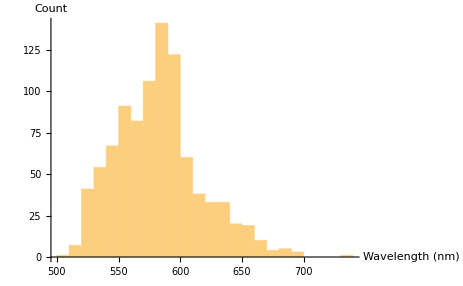

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_originalmesh_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
engfac=100/(QuantityMagnitude[TotalEnergy[data]])
temp=engfac AssumedTemprature[data,0.23*1000]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.6,5];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
WavelengthHist[data]
```

### Original with Mirror

-Graphics-

2.77516×10^-16 J

2.42404×10^-9 W/m^2

-Graphics-

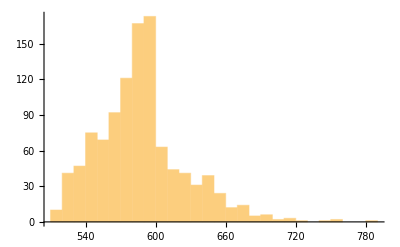

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_mirrororiginal_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.6,5];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
WavelengthHist[data]
```

### Changed Heights

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_originalmesh_H8_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.8,5];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
```

-Graphics-

2.84742×10^-16 J

2.31593×10^-9 W/m^2

-Graphics-

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_originalmesh_H10_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[1,5];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
```

-Graphics-

2.83244×10^-16 J

2.15648×10^-9 W/m^2

-Graphics-

### Changed Widths

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_originalmesh_W6_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.8,6];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
```

-Graphics-

3.07267×10^-16 J

2.30179×10^-9 W/m^2

-Graphics-

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_originalmesh_W7_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.8,7];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
```

-Graphics-

3.06477×10^-16 J

2.12924×10^-9 W/m^2

-Graphics-

### Optimum

-Graphics-

3.9553×10^-16 J

33.3725 mm^2

2.96299×10^-9 W/m^2

-Graphics-

2.26535×10^16

35.7711 K

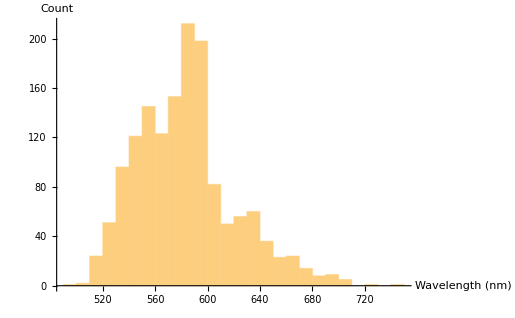

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_optimummesh_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.8,6]
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
engfac=100/(QuantityMagnitude[TotalEnergy[data]])
temp=engfac AssumedTemprature[data,0.36*1000]
WavelengthHist[data]
```

### Changed Shapes

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_fishtailmesh_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.6,5];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
```

-Graphics-

8.09017×10^-17 J

7.06658×10^-10 W/m^2

-Graphics-

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_fishtailcurvemesh_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.6,5];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
```

-Graphics-

9.60075×10^-17 J

8.38604×10^-10 W/m^2

-Graphics-

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_mirrorfishtail_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.6,5];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
```

-Graphics-

6.98876×10^-17 J

6.10453×10^-10 W/m^2

-Graphics-

-Graphics-

1.79935×10^-16 J

1.57169×10^-9 W/m^2

-Graphics-

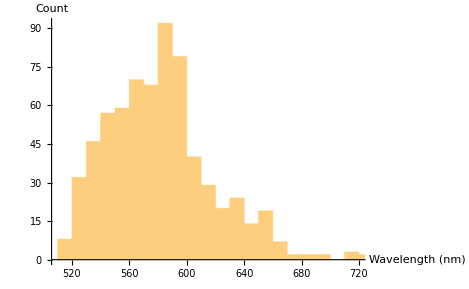

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_with20PLQY_fanmesh_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.6,5];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
WavelengthHist[data]
```

-Graphics-

3.07589×10^-16 J

3.91635×10^-9 W/m^2

-Graphics-

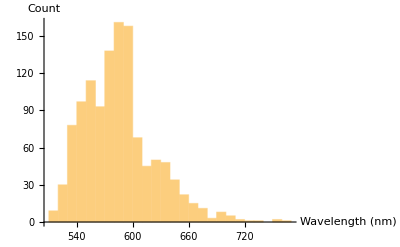

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_cylinder_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=Quantity[Pi 2.5^2,"Millimeters"^2];
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
WavelengthHist[data]
```

-Graphics-

2.24791×10^-17 J

2862.12 mm^2

1.9635×10^-12 W/m^2

-Graphics-

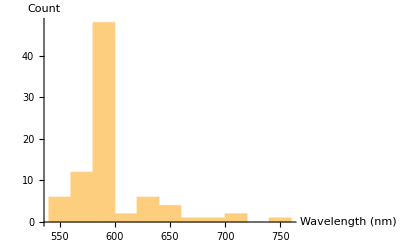

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_originalmesh_10x_10000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=100*OutputArea[0.6,5]
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
WavelengthHist[data]
```

```mathematica
data=Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_water_withPLQY_originalmesh_100000.csv"],{2}];
output=PrepareData[data];
chart= DataCount[output];
VisualiseData[chart]
energy=TotalUsefulEnergy[data]
area=OutputArea[0.6,5]
flux=Irradiance[energy,area]
echart=EnergyChart[data];
VisualiseEnergy[echart]
```

-Graphics-

1.53886×10^-15 J

28.6212 mm^2

1.34416×10^-8 W/m^2

-Graphics-